## Dodelson 8.12

Show that the cross-terms from the monopole and dipole vanish.

```mathematica
Print["The integral : ",tmp=HoldForm[∫_0^∞ SphericalBesselJ[l,x]SphericalBesselJ[l,x]ⅆx]," => ",jjl=Refine[tmp//ReleaseHold,l>=0]
];
jj[ll_]:=jjl/.l->ll;
```

The integral : ∫_0^∞ SphericalBesselJ[l,x] SphericalBesselJ[l,x]ⅆx => π/(2+4 l)

```mathematica
Print["The integral : ",tmp=HoldForm[∫_0^∞ SphericalBesselJ[l,x]D[SphericalBesselJ[l,x],x]ⅆx]," => ",
jdjl=Refine[tmp//ReleaseHold,l>0]
];
jdj[ll_]:=jdjl/.l->ll
```

The integral : ∫_0^∞ SphericalBesselJ[l,x] ∂_x SphericalBesselJ[l,x]ⅆx => 0

```mathematica
Print["The integral : ",tmp=HoldForm[∫_0^∞ D[SphericalBesselJ[l,x],x]D[SphericalBesselJ[l,x],x]ⅆx]," => ",
djdjl=Refine[tmp//ReleaseHold,l>1]];
djdj[ll_]:=djdjl/.l->ll
```

The integral : ∫_0^∞ ∂_x SphericalBesselJ[l,x] ∂_x SphericalBesselJ[l,x]ⅆx => ((-1+2 l+2 l^2) π)/(2 (-3-2 l+12 l^2+8 l^3))

Plotting these functions over l=[10,50] =>

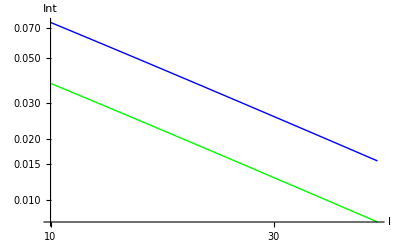

```mathematica
Print["Plotting these functions over l=[10,50] =>"];LogLogPlot[Tooltip[{jj[l],jdj[l],djdj[l]}],{l,10,50},AxesLabel->{l,Int},PlotStyle->{Directive[Blue,PointSize[Large]],Red,Green}]
```